```mathematica
p[z_]=(z^2-1)(z-λ); lp[z_]=p[z]p''[z]/p'[z]/p'[z];sp[z_]=z-1/(1-lp[z])p[z]/p'[z]; soluciones=Solve[-2 (λ+λ^3)+(3+9 λ^2) z-12 λ z^2+(3+λ^2) z^3==0,z];
r0=1.;r1=-1.;r2=λ;
rootPosition := Compile[{{z,_Complex}},
    Which[Abs[z -r0] <  10.0^(-6),3,
Abs[z-r1]<10.0^(-6), 2,
Abs[z-r2]<10.0^(-6), 1,
    True, 0],
{{rootf[_],_Complex}}
]
iterSchLambda = Compile[{{z, _Complex},{ λ,_Complex}},(4 z^3+λ-10 z^2 λ+z^4 λ+4 z λ^2)/(1+3 z^4-4 z λ-4 z^3 λ+2 λ^2+2 z^2 λ^2)];
iterColorAlgorithm[iterMethod_,x_,y_,lim_] :=
    Block[{z,λ,ct,r}, z =z/.soluciones[[3]];
λ= x + y I; ct = 0;r = rootPosition[z];
raiz1=0;
        While[(r==0) && (ct < lim),
            ++ct; z = iterMethod[z,λ];r = rootPosition[z]
	       ];
	raiz1=N[r];	    

		  
z =z/.soluciones[[2]];λ= x + y I; ct = 0;r = rootPosition[z];
     raiz2=0   ;
While[(r==0) && (ct < lim),
            ++ct; z = iterMethod[z,λ];r = rootPosition[z]
	       ];
	raiz2=N[r];	    

z =z/.soluciones[[1]];λ= x + y I; ct = 0;r = rootPosition[z];
     raiz3=0;  
 While[(r==0) && (ct < lim),
            ++ct; z = iterMethod[z,λ];r = rootPosition[z]
	       ];
	raiz3=N[r];	    

	Return[N[(raiz3)*16+(raiz2)*4+raiz1]](*Devuelve un numero del 0 al 80 que marcará el color*)

    ]
Clear[fractalColorWS]
fractalColorWS[p_] :=
Switch[IntegerPart[p],
64, RGBColor[1,1,1],
0,Black,1,Hue[0.015625],2,Hue[0.03125],3,Hue[0.046875],4,Hue[0.0625],5,Hue[0.078125],6,Hue[0.09375],7,Hue[0.109375],8,Hue[0.125],9,Hue[0.140625],10,Hue[0.15625],11,Hue[0.171875],12,Hue[0.1875],13,Hue[0.203125],14,Hue[0.21875],15,Hue[0.234375],16,Hue[0.25],17,Hue[0.265625],18,Hue[0.28125],19,Hue[0.296875],20,Hue[0.3125],21,Hue[0.328125],22,Hue[0.34375],23,Hue[0.359375],24,Hue[0.375],25,Hue[0.390625],26,Hue[0.40625],27,Hue[0.421875],28,Hue[0.4375],29,Hue[0.453125],30,Hue[0.46875],31,Hue[0.484375],32,Hue[0.5],33,Hue[0.515625],34,Hue[0.53125],35,Hue[0.546875],36,Hue[0.5625],37,Hue[0.578125],38,Hue[0.59375],39,Hue[0.609375],40,Hue[0.625],41,Hue[0.640625],42,Hue[0.65625],43,Hue[0.671875],44,Hue[0.6875],45,Hue[0.703125],46,Hue[0.71875],47,Hue[0.734375],48,Hue[0.75],49,Hue[0.765625],50,Hue[0.78125],51,Hue[0.796875],52,Hue[0.8125],53,Hue[0.828125],54,Hue[0.84375],55,Hue[0.859375],56,Hue[0.875],57,Hue[0.890625],58,Hue[0.90625],59,Hue[0.921875],60,Hue[0.9375],61,Hue[0.953125],62,Hue[0.96875],63,Hue[0.984375]


]
ft[min_,max_,pt_,nTicks_]:=Block[{taux,j,stepTicks=(max-min)/(nTicks-1)},
taux=Table[{pt*(j-1)/(nTicks-1)+1,min+(j-1)*stepTicks},{j,1,nTicks}]
]
Clear[plotColorFractal]
plotColorFractal[iterMethod_,points_]:=
Block[{$Messages = {},
stepx=(xxMax-xxMin)/points,stepy=(yyMax-yyMin)/points},
ArrayPlot[Table[iterColorAlgorithm[iterMethod,x,y,limIterations],
{y,yyMax,1.00001*yyMin,-stepy},
{x,xxMin,1.00001*xxMax,stepx}],
FrameTicks->{ft[yyMax,yyMin,points,5],ft[xxMin,xxMax,points,5]},
PlotRange->{0,65},(* Three roots + fixed  *)
ColorFunctionScaling->False,
ColorFunction->fractalColorWS
]
]
Off[General::ovfl];    Off[General::unfl];    Off[Infinity::indet]
Off[CompiledFunction::cccx];    Off[CompiledFunction::cfn]; Off[CompiledFunction::cfcx];    Off[CompiledFunction::cfex]; Off[CompiledFunction::crcx];    Off[CompiledFunction::cfse]; Off[CompiledFunction::ilsm];    Off[CompiledFunction::cfsa]
```

```mathematica
numberPoints =512;limIterations=100;
xxMin=-500; xxMax=500; yyMin=-500; yyMax=500;plotColorFractal[iterSchLambda, numberPoints]
```

-Graphics-

```mathematica
numberPoints =512;limIterations=100;
xxMin=-50; xxMax=50; yyMin=100; yyMax=200;plotColorFractal[iterSchLambda, numberPoints]
```

-Graphics-

```mathematica
numberPoints =512;limIterations=100;
xxMin=-5; xxMax=5; yyMin=135; yyMax=155;plotColorFractal[iterSchLambda, numberPoints]
```

-Graphics-

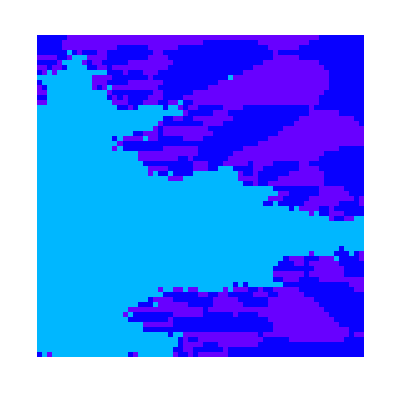

```mathematica
numberPoints =64;limIterations=50;
xxMin=3; xxMax=3.5; yyMin=142.5; yyMax=575/4;plotColorFractal[iterSchLambda, numberPoints]
```